```mathematica
sample=RandomReal[{100,300},{5,10}];
```

```mathematica
quotes=Module[{array={}},Do[AppendTo[array,Table[(sample⟦j,i⟧-sample⟦j,i-1⟧)/sample⟦j,i-1⟧,{i,2,Length@sample⟦1⟧}]],{j,1,5}];array];
```

```mathematica
return=Mean[#]&/@quotes
```

{0.00798506,0.0877875,0.113584,0.123004,0.126395}

```mathematica
covMatrix=Covariance[quotes//Transpose];
```

```mathematica
l={1,1,1,1,1}
```

{1,1,1,1,1}

```mathematica
h0=(Inverse[covMatrix].l)/(l.Inverse[covMatrix].l)
```

{0.498677,0.288232,0.44741,0.124335,-0.358655}

```mathematica
h1=(Inverse[covMatrix].return)-Inverse[covMatrix].l*(l.Inverse[covMatrix].return)/(l.Inverse[covMatrix].l)
```

{-0.913909,0.116787,-0.118569,0.164456,0.751235}

```mathematica
α0=return.h0;
α1=return.h1;
β0=h0.covMatrix.h0;
```

```mathematica
α0
```

0.0500654

```mathematica
f[x_]:=√(α1*(x-β0))+α0
```

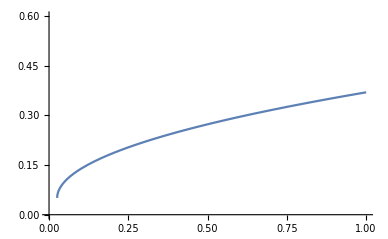

```mathematica
Plot[f[x],{x,0,1},PlotRange->{Automatic,{0,0.6}}]
```

```mathematica
fun[x_]:=x.return
```

```mathematica
sol=Minimize[{-fun[{x1,x2,x3,x4,x5}],{x1,x2,x3,x4,x5}.l==1,{x1,x2,x3,x4,x5}.covMatrix.{x1,x2,x3,x4,x5}<=0.09,x1≥0,x2≥0,x3≥0,x4≥0,x5≥0},{x1,x2,x3,x4,x5}]
```

{-0.115541,{x1→-2.809×10^-7,x2→0.155965,x3→0.288557,x4→0.335049,x5→0.220431}}

```mathematica
rf=0.0037;
```

```mathematica
fun[x_]:=(x.return-rf)/(x.covMatrix.x)
```

```mathematica
sol1=Minimize[{-fun[{x1,x2,x3,x4,x5}],{x1,x2,x3,x4,x5}.l==1,x1≥0,x2≥0.05,x3≥0,x4≥0,x5≥0},{x1,x2,x3,x4,x5}]
```

{-0.124464,{x1→0.,x2→0.05,x3→0.,x4→0.,x5→0.95}}

```mathematica
w=(sol1⟦2⟧//Values)
```

{0.,0.05,0.,0.,0.95}

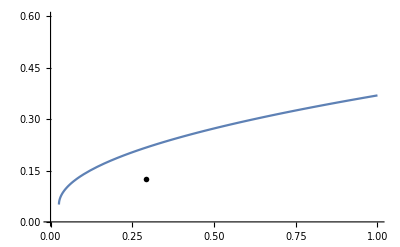

```mathematica
Show[{Plot[f[x],{x,0,1},PlotRange->{Automatic,{0,0.6}}],Graphics[{PointSize[0.01],Point[{w.covMatrix.w,w.return}]}]}]
```